### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
constraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_]:={α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0}
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
Get["stableRegionsEq.mx"]
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

Opti7-1-19-21-27-57

{0.237367,-3.3879,2.6848,4.8082,-3.08849,-0.318696,0.197218,0.93276,0.278756,-0.0500818,0.0356668,0.0542897,0.533706,0.0246289,-2.65414,-1.74384,4.39785,-0.179519,-0.444092,-1.46281,1.34961,0.569727,-1.65974,2.1082,-1.32077,2.19013,0.0964213,0.03421,-1.68387,1.4274,0.570474,0.686,1.0599,-1.61789,0.253343,0.304647,2.68387,-1.4274,-0.570474,-0.686,-3.95685,3.1909,-0.56318,1.32913}

{True,True,True,False,False,True,True,False,False,True,True,True,True,False,True,False,True,True,True,True,False,False,False,True,False}

12.5755

-Graphics3D-

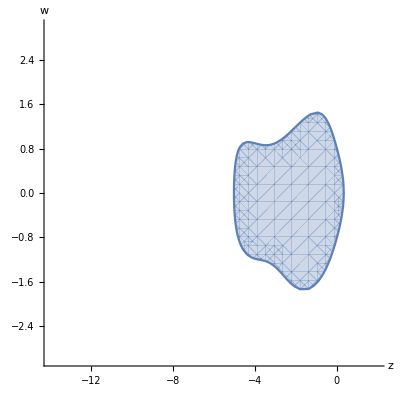

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.23736702338950375,-3.3879031976141665,2.6847957809459526,4.8081988966320885,-3.088487626304453,-0.31869551018307113,0.19721773165820847,0.9327595212359623,0.27875585047425205,-0.0500818445908907,0.03566681987533908,0.0542896692773617,0.5337060634581391,0.02462893345907009,-2.6541363815798014,-1.7438432450993013,4.397850294203606,-0.17951888922920461,-0.4440920306177633,-1.4628133767237455,1.3496073953741128,0.5697273416539671,-1.6597405620043353,2.1082016526098073,-1.3207660033294872,2.1901347611126782,0.09642125537893914,0.03420998683786982,-1.6838707233490107,1.4273972250978673,0.5704739579799685,0.685999540271175,1.059899911336994,-1.6178897785927493,0.25334293841387706,0.3046469288418783,2.6838707233490102,-1.4273972250978644,-0.5704739579799699,-0.6859995402711753,-3.9568500656066945,3.1909048716723882,-0.5631801607787009,1.3291253547130073}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti7-1-17-06-38-41

{0.346864,0.635706,0.0417548,0.112123,-3.99344,-1.58842,0.835727,1.46643,-0.00590044,-3.26756,2.48725,-1.27233,0.948278,1.88744,-0.0448832,-1.84159,0.543749,-1.54751,0.914181,0.818153,-0.798609,-1.73725,2.07049,-1.6253,0.56542,-0.06615,0.530617,-0.0298868,-0.749076,0.484263,0.908438,0.356375,0.505097,0.651171,-0.830477,-0.325791,1.74908,-0.484263,-0.908438,-0.356375,-2.11582,0.986211,0.425394,0.704215}

{True,True,True,True,True,True,True,True,False,True,True,True,True,False,True,False,True,True,True,True,True,True,True,True,False}

13.2339

-Graphics3D-

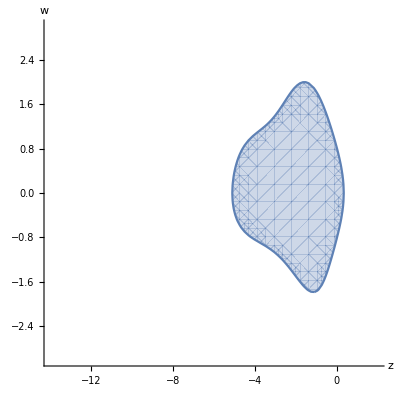

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.3468637234361462,0.6357060807521794,0.041754838891117675,0.11212330695064389,-3.993437409330635,-1.5884247381228052,0.835727137309742,1.4664287559538236,-0.005900440928510632,-3.2675627015417543,2.487250425854031,-1.2723324796679367,0.9482776700756552,1.8874370798985904,-0.04488321517987302,-1.8415895042043018,0.5437490988269468,-1.5475059535042817,0.9141811293774019,0.8181531617763057,-0.7986088802105423,-1.7372486424978264,2.0704873653456968,-1.6253012256336876,0.5654197424004141,-0.06614995342515217,0.5306169687460796,-0.029886757721341466,-0.749075864141922,0.48426281642017077,0.9084381064360679,0.35637494128568326,0.5050970207527302,0.6511711996648143,-0.8304769741111933,-0.32579124630635126,1.7490758641419226,-0.4842628164201708,-0.9084381064360685,-0.3563749412856834,-2.1158195286897667,0.9862110540243946,0.42539366556230856,0.7042148091030636}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti7-1-14-09-46-17

{0.00393695,-2.09709,2.348,-1.06372,0.943585,4.98162,0.165281,4.76767,-4.28,-2.01178,-0.228295,0.375374,-0.0479527,2.1471,-0.784726,-2.89285,2.97942,1.86117,0.406548,-2.03387,0.921643,0.334461,0.53403,-0.6622,-0.631759,0.895282,0.668875,0.0676019,-1.07701,1.72104,0.586353,-0.230385,-1.61533,1.76005,-0.23838,0.0936625,2.07701,-1.72104,-0.586353,0.230385,-4.76052,2.98454,1.19811,0.577878}

{True,True,False,False,True,False,True,False,False,True,True,True,True,False,True,False,True,False,True,True,False,False,False,True,False}

6.4436

-Graphics3D-

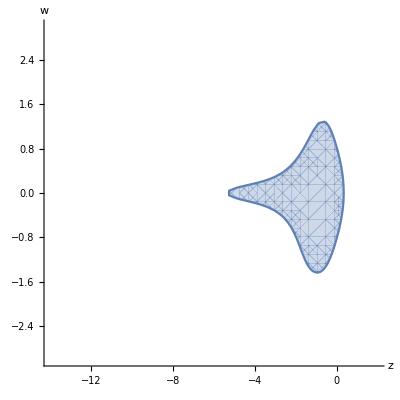

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.0039369547162335546,-2.0970913064530743,2.348004562684913,-1.0637176906005426,0.9435851279805889,4.981618861663432,0.16528093697476984,4.767668250907717,-4.279999067155958,-2.011776641541188,-0.22829528668668134,0.37537432896068335,-0.04795265836477372,2.147104174281902,-0.7847263875958536,-2.892847199716452,2.979417163320809,1.8611693964631457,0.4065475826699378,-2.0338713108704254,0.9216427248707508,0.3344608109390388,0.5340300061938158,-0.662200282521448,-0.6317590981646451,0.8952823157004709,0.6688748762491636,0.06760190621501072,-1.0770074908486977,1.7210399063939419,0.5863527838459761,-0.23038519939122026,-1.6153343023123372,1.7600520632812753,-0.23838030686437015,0.09366254589543212,2.0770074908486986,-1.7210399063939426,-0.5863527838459762,0.2303851993912201,-4.760523948499409,2.984539888183993,1.1981063857874676,0.5778776745279484}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-12-24-14-43-33

{0.0335821,-0.837558,1.66896,-3.02199,-0.0231945,-1.28897,0.0669707,-1.01456,0.615095,1.33323,4.32264,-0.10617,0.0662565,4.2937,-1.18,0.877782,-0.993349,-3.49751,-0.258787,0.741099,-1.2259,-0.589544,4.47264,-1.67813,1.58592,-0.766194,0.253035,-0.0727608,-0.544446,1.16903,0.195273,0.180138,3.4645,-3.56165,0.0505341,0.0466175,1.54445,-1.16903,-0.195273,-0.180138,0.197485,-3.97076,3.47522,0.298059}

{True,True,False,False,True,True,True,False,False,True,True,True,True,True,True,True,True,False,True,True,False,False,False,True,False}

14.3071

-Graphics3D-

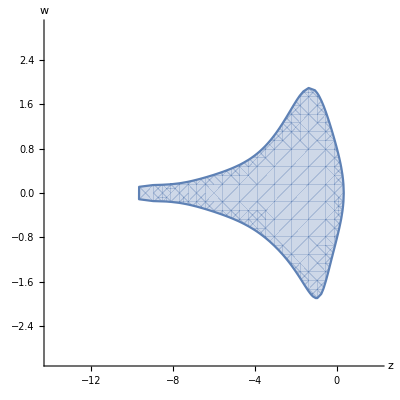

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]

Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.033582117125222785,-0.8375581437820365,1.668959247419533,-3.0219872156212277,-0.02319448968660813,-1.2889724638358064,0.06697069480042099,-1.014555796025963,0.6150945951470154,1.3332285713098808,4.322636862455755,-0.10616981938752963,0.06625645773496461,4.293697866812735,-1.1800010590695766,0.877781853670548,-0.9933491720920042,-3.497505112296517,-0.2587869679879975,0.7410988679036021,-1.2259012157437108,-0.5895440272307872,4.472640351080325,-1.6781263226759247,1.5859191174660352,-0.7661935983747827,0.2530352938181505,-0.07276081290940295,-0.5444455732458032,1.1690341851303316,0.19527304488870784,0.1801383432267639,3.4644998310729336,-3.5616514059515008,0.050534119216531816,0.04661745566203546,1.544445573245803,-1.1690341851303312,-0.19527304488870786,-0.1801383432267639,0.19748498088374386,-3.970761385278509,3.475216994015969,0.2980594103787962}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-12-11-10-01-47: SRIOpt1

{-0.0419922,2.84261,-2.05277,4.33824,-2.88959,2.30176,0.262043,0.209036,-0.150238,0.058366,0.614944,0.0853512,-0.216411,1.53364,0.260662,-1.0536,1.70153,-0.207257,-0.511901,2.67767,-4.9395,0.15581,3.23616,-1.42231,1.1401,-0.640133,0.47363,0.0264045,-1.84535,2.68876,-0.252387,0.408969,0.496966,-0.57712,-0.129197,0.209351,2.84535,-2.68876,0.252387,-0.408969,0.115227,-0.578771,0.285785,0.177759}

{True,True,False,False,False,False,True,False,True,True,True,True,True,False,True,True,True,False,True,True,False,False,False,True,False}

22.1099

-Graphics3D-

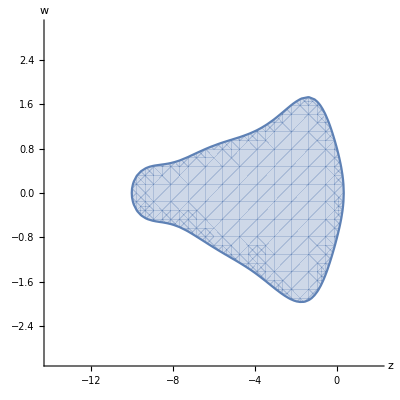

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{-0.04199224421316468,2.842612915017106,-2.0527723684000727,4.338237071435815,-2.8895936137439793,2.3017575594644466,0.26204282091330466,0.20903646383505375,-0.1502377115150361,0.05836595312746999,0.6149440396332373,0.08535117634046772,-0.21641093549612528,1.5336352863679572,0.26066223492647056,-1.0536037558179159,1.7015284721089472,-0.20725685784180017,-0.5119011827621657,2.67767339866713,-4.9395031322250995,0.15580956238299215,3.2361551006624674,-1.4223118283355949,1.140099274172029,-0.6401334255743456,0.4736296532772559,0.026404498125060714,-1.8453464565104432,2.688764531100726,-0.2523866501071323,0.40896857551684956,0.4969658141589478,-0.5771202869753592,-0.12919702470322217,0.2093514975196336,2.8453464565104425,-2.688764531100725,0.2523866501071322,-0.40896857551684945,0.11522663875443433,-0.57877086147738,0.2857851028163886,0.17775911990655704}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-12-11-10-01-47

{-0.073484,1.52566,-0.670504,0.0000948043,2.02246,1.13567,0.208254,0.605364,0.674189,-0.182143,0.577765,-0.260079,0.278867,-1.72512,3.65283,-0.913961,2.29509,0.246419,0.456348,0.579991,-1.10265,-3.88329,2.25651,0.227933,-0.246126,0.833896,0.321587,0.0906431,-1.25712,1.45917,0.513951,0.283999,-1.16127,1.52542,-0.234541,-0.129602,2.25712,-1.45917,-0.513951,-0.283999,-2.54607,2.12607,-0.436789,0.856789}

{True,True,True,True,False,False,True,False,False,True,True,True,True,False,True,True,True,False,True,True,False,False,False,True,False}

16.3895

-Graphics3D-

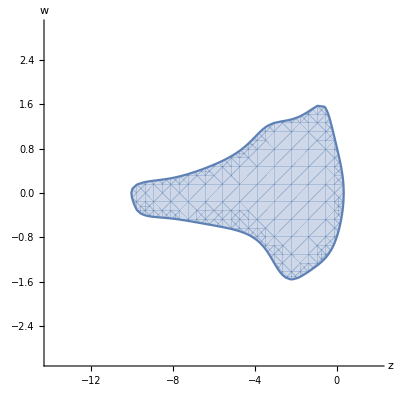

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{-0.07348399551163982,1.5256599546111518,-0.6705035441237552,9.480427009263596*^-5,2.022458057732523,1.1356664038963942,0.2082538206656805,0.6053635635011927,0.674189080905125,-0.18214314337463292,0.5777647062431013,-0.2600787803961824,0.2788666936077316,-1.725119276977833,3.652834686299483,-0.9139606793813797,2.2950881321697305,0.24641947102224088,0.45634835451185823,0.5799913339726462,-1.1026477206612013,-3.883291233400686,2.2565063578875124,0.2279325074123351,-0.24612596847299933,0.8338958083161195,0.32158707098085093,0.09064308917602902,-1.2571247020191898,1.4591749994820709,0.5139509089451423,0.2839987935919767,-1.1612732945043358,1.5254163282403768,-0.23454065159698947,-0.12960238213905145,2.2571247020191896,-1.4591749994820704,-0.5139509089451424,-0.2839987935919767,-2.546074498639557,2.1260746663604104,-0.4367891701128453,0.8567890023919921}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-8-15-11-23-21

{0.0875631,-0.120725,0.674978,-1.4283,1.90984,4.77767,0.0370201,-0.639499,2.62577,0.406836,-2.481,0.00792599,-0.00230713,2.87462,-1.38522,-3.248,-1.19774,4.15159,0.192406,1.89896,-2.84346,-2.88537,4.66074,-0.726623,-0.0589055,0.36562,0.67549,0.0177959,-2.15764,2.18551,0.722452,0.249678,-4.58979,4.77683,-0.139004,-0.0480396,3.15764,-2.18551,-0.722452,-0.249678,-1.71247,-0.311985,1.03505,0.989405}

{True,True,False,False,True,False,True,False,True,True,True,True,True,True,True,False,True,False,True,True,False,False,False,True,False}

19.0846

-Graphics3D-

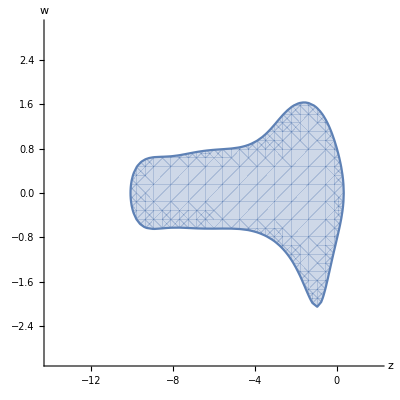

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.08756308925148616,-0.12072472929099624,0.6749783675307094,-1.4283024447189836,1.909842174518423,4.777673160798434,0.03702011651575981,-0.6394992501689805,2.625770633002624,0.406835668871614,-2.480996086483515,0.007925985415054449,-0.002307126303610374,2.8746249300089146,-1.3852197598555909,-3.247999939062163,-1.1977436724829615,4.15158786148627,0.19240612390399545,1.8989591775565158,-2.843456193650939,-2.8853705806505237,4.660735134323289,-0.726622700103415,-0.05890548884183365,0.3656195891670018,0.6754899991036113,0.01779590057122051,-2.1576418608441825,2.1855115725871888,0.7224520616985962,0.24967822655839744,-4.589790140136851,4.776833960830054,-0.13900420089787732,-0.048039619795324784,3.1576418608441683,-2.185511572587175,-0.722452061698596,-0.24967822655839758,-1.7124718327729864,-0.3119847063538952,1.0350513260839882,0.9894052130428934}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-8-4-03-54-23

{0.00066236,1.62716,-1.04641,1.65938,-1.6356,1.16269,0.0632166,1.04175,0.887664,-3.30158,3.04384,-0.0527684,0.00478832,4.90709,-3.36703,-4.09437,4.78226,0.677771,0.251429,-1.14717,-0.204363,1.21496,0.440621,-0.514558,0.783776,-0.455155,0.489126,0.182253,-1.75638,2.27962,0.448198,0.0285647,-3.28423,3.4041,-0.11269,-0.00718199,2.75638,-2.27962,-0.448198,-0.0285647,2.34613,-3.93974,0.332105,1.26151}

{True,True,False,True,True,False,True,False,True,True,True,True,True,False,True,False,True,False,True,True,False,False,False,True,False}

10.3227

-Graphics3D-

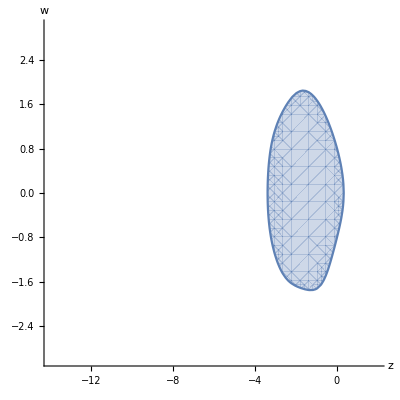

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.0006623601686593163,1.6271637862140707,-1.0464074390309193,1.6593758580474987,-1.6355958030783295,1.1626949600695773,0.06321655695942992,1.041753515564928,0.8876636009653156,-3.3015809369852156,3.043838625384488,-0.052768354198057595,0.004788317127144488,4.907091250786488,-3.3670295810289517,-4.094371691164077,4.782261578760532,0.6777707373275506,0.25142902966728037,-1.1471736222359803,-0.20436309161312902,1.2149649619017644,0.4406210738383759,-0.514557544493714,0.7837760744997847,-0.4551547360619151,0.48912564021637517,0.1822530213457552,-1.7563808899347557,2.27961868204339,0.4481975330905559,0.028564674800809906,-3.2842313059963044,3.404103165308461,-0.11268987084422699,-0.007181988467929532,2.7563808899347566,-2.279618682043391,-0.4481975330905558,-0.028564674800809986,2.3461291653337386,-3.939743394371634,0.33210500528160963,1.2615092237562857}]

higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-7-30-07-46-45

{0.257964,2.08966,-2.63261,3.82324,-1.59793,-0.548278,0.254123,-0.60148,-0.0145143,2.85715,0.383979,-0.267681,0.910133,3.10241,-1.83319,-1.16787,-2.77089,-1.26964,0.504106,-2.0261,1.23372,2.14023,-0.784542,0.0787595,-0.305079,1.4511,-0.166914,0.0208969,0.977039,-0.807428,0.352126,0.478263,-1.97213,2.39074,-0.177509,-0.241096,0.0229611,0.807428,-0.352126,-0.478263,-4.14328,2.24624,1.73051,0.166529}

{True,True,True,True,True,False,True,False,False,True,True,True,True,True,True,False,True,False,True,True,False,False,False,True,False}

20.769

-Graphics3D-

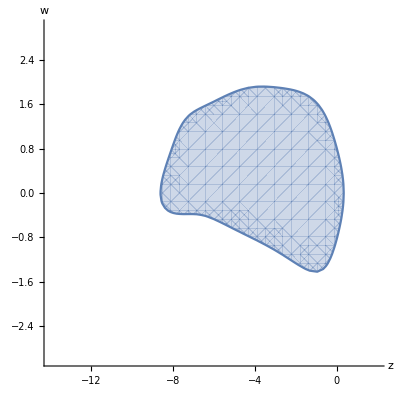

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.2579635226098418,2.0896611070246767,-2.6326093689177608,3.823238007305252,-1.5979327769988472,-0.5482779853959228,0.25412300869774895,-0.6014795250221303,-0.014514318241438277,2.857154070729542,0.38397899499872096,-0.26768100055583494,0.9101327429759887,3.1024114699521617,-1.833192115924115,-1.1678675158367648,-2.7708935017197893,-1.2696435321104458,0.5041061482443443,-2.0261010186429895,1.2337237977852462,2.1402347738616387,-0.7845424103247053,0.0787595322677016,-0.30507902873028114,1.4510957686142136,-0.1669136770864341,0.020896937202501617,0.977038876662149,-0.8074280390583765,0.35212574850644657,0.47826341388978094,-1.9721343485230134,2.390738630722423,-0.17750875477724132,-0.24109552742216825,0.022961123337851053,0.8074280390583765,-0.35212574850644657,-0.47826341388978094,-4.14327586735318,2.246235398331404,1.7305119387360715,0.16652853028570502}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-7-25-03-24-12

{0.0568408,-0.40253,1.19721,0.944003,-2.95063,-4.52708,0.271787,1.3758,0.703801,-1.15152,-0.610455,-0.256753,0.159716,4.2717,-2.36792,2.76337,0.259273,-4.99988,0.521331,1.76315,-0.525566,-2.90794,1.44613,0.545573,-0.411521,1.00344,0.42427,-0.0161936,1.7421,-1.78843,0.878001,0.168334,-2.30504,2.85053,-0.45773,-0.0877579,-0.742099,1.78843,-0.878001,-0.168334,-1.12928,-0.69877,0.946788,0.881261}

{True,True,False,True,True,False,True,False,True,True,True,True,True,False,True,True,True,False,True,True,False,False,False,True,False}

11.9636

-Graphics3D-

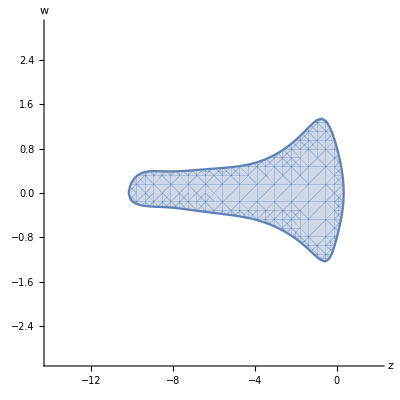

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.056840785581052405,-0.4025300540575041,1.197211249236612,0.9440025996837822,-2.9506255903525296,-4.527076548899104,0.2717865191599552,1.3758017758918157,0.7038010224675545,-1.1515214748666933,-0.610455049579449,-0.25675340357820037,0.15971574786080606,4.271702366286397,-2.367924959112803,2.763373774938453,0.25927297643151065,-4.999876539028702,0.521331486829594,1.7631504128808166,-0.5255664112098525,-2.9079354119185705,1.4461309289274842,0.5455725474787088,-0.4115209932689666,1.0034445686381097,0.4242700103460238,-0.016193585715166946,1.7420986792909956,-1.788433951834226,0.8780010819478139,0.16833419059541657,-2.3050447695488865,2.850532292906097,-0.457729609489846,-0.08775791386736463,-0.7420986792909963,1.7884339518342265,-0.8780010819478138,-0.16833419059541638,-1.1292790354780207,-0.6987702882234114,0.9467884827919373,0.8812608409094945}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```

Opti6-7-23-09-30-00

{0.0687915,-2.6514,3.78579,0.0770047,-1.31882,0.362632,0.0503382,0.490063,-1.1285,-0.376874,3.49982,-0.553599,0.135409,1.85707,-0.753809,2.30001,0.802366,1.45121,-0.224362,1.50674,-2.02777,3.67976,-1.85835,0.018221,-2.65275,3.31931,0.280505,0.0529397,-1.83816,2.80962,-0.244791,0.273332,3.82031,-3.82672,-0.0549217,0.0613252,2.83816,-2.80962,0.244791,-0.273332,-1.80574,-0.439676,1.79161,0.4538}

{True,True,False,False,True,False,True,True,False,True,True,True,True,False,True,False,True,False,True,True,False,False,False,True,False}

15.9764

-Graphics3D-

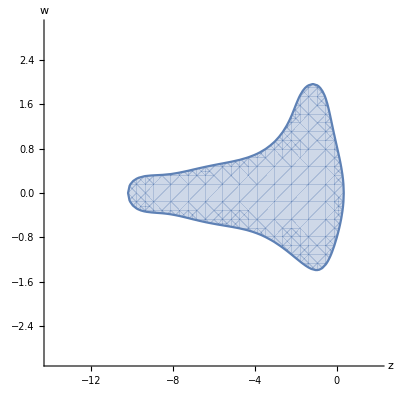

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Set[{A021,A031,A032,A041,A042,A043,A121,A131,A132,A141,A142,A143,B021,B031,B032,B041,B042,B043,B121,B131,B132,B141,B142,B143,α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44},{0.06879145695381707,-2.651400823411187,3.785794679906524,0.07700473413524146,-1.318816254815736,0.3626324894225006,0.05033821923219472,0.4900634849523661,-1.1285047144321152,-0.3768741344300891,3.4998199624261805,-0.553598655218657,0.1354092299398354,1.857066784161747,-0.7538094262338756,2.3000126352984966,0.80236620768309,1.4512079916501448,-0.2243618043076717,1.5067433970457584,-2.0277671708273672,3.6797561347870213,-1.8583457825605938,0.018221029213194493,-2.652750678708339,3.3193054969092017,0.28050544092040103,0.05293974087873617,-1.8381611585192685,2.8096204425250004,-0.24479099110884792,0.27333170710311616,3.8203116793032934,-3.826715125839997,-0.05492174844344777,0.061325194980151446,2.8381611585192674,-2.8096204425249995,0.24479099110884806,-0.2733317071031161,-1.8057359471564547,-0.43967575992714536,1.7916112304908611,0.453800476592739}]
higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,-4,4},{w,wmin,3},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None]
```